## Numerical Analysis — Problem Set 7 — Standard Deviation and r-Value

## Due Tuesday, Nov. 1 (beginning of class)

We are going to work with Aaron Judge’s run-value-weighted Offensive Batting Average (rOBA) as found on Max’s Problem Set 6. Max had the following table:

```mathematica
data = {{"Year", "Average"},{2016,0.272},{2017,0.435},{2018,0.396},{2019,0.393},{2020,0.379},{2021,0.392},{2022,0.463}};Grid[data]
```

Year | Average
2016 | 0.272
2017 | 0.435
2018 | 0.396
2019 | 0.393
2020 | 0.379
2021 | 0.392
2022 | 0.463

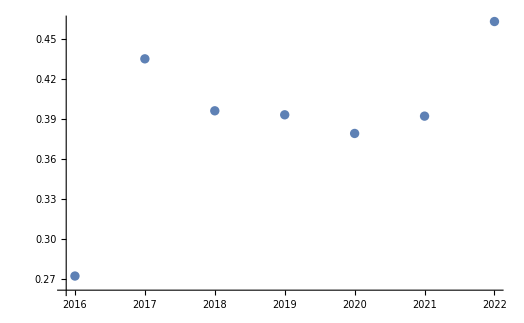

```mathematica
ListPlot[Drop[data]]
```

Let’s ignore the years for a moment:

```mathematica
battingAverages =Transpose[ Drop[data, 1]][[2]]
```

{0.272,0.435,0.396,0.393,0.379,0.392,0.463}

### 1. Mean and Total Deviation of the Batting Averages

(a) There are 7 numbers in the battingAverages list at the bottom of the previous page. The first thing to do is calculate their mean. “Mean” is a fancy word for average commonly used in the world of statistics. So I am asking you to take an average of seven things (which themselves are averages). So you just add the seven numbers up and divide by 7. Store the average in some register (for example R0). You will use the average a lot in the next part and you don’t want to have to type it in over and over again.

(b) Make a new list from the original list. For each number in the old list, you just subtract the mean you stored in R0 to get the corresponding number in the new list. Record that list as your answer to this part.

(c) This new list tells you how much each number in the original list deviates from the mean. You could add up all the numbers in this new list to find the total deviation. Do that. The answer may surprise you.

(d) Try it again with a different list to make sure that the surprise wasn’t an accident. We’ll use this list, {20, 40, 50, 65, 15, 8}, of six numbers. Find its mean. Store that in R1 so that you can use it repeatedly.

(e) Subtract the mean you stored in R1 from each number in the list. This is the list of deviations from the mean.

(f) Sum up the deviations. The surprise is not an accident.

### 2. Variance of the Batting Averages

From 1(c) and 1(f), you are starting to get the idea that summing up the deviations is useless. The total deviation is always going to be 0.

(a) From the list in 1(b) make another list by squaring each of the numbers.

(b) Sum up the numbers you got in 2(a). Divide it by 7. This is called the variance.

The truth is, if you are a serious statistician, you don’t divide by 7. You divide by 6. That is because the 7 deviations are not independent. They add up to 0, so of course they are not fully independent! One of the deviations is somehow redundant. The upshot of this redundancy is that you don’t have 7 estimates of the variance. You really only have 6.

(c) Sum up the numbers you got in 2(a) again. Divide it by 6. This is what statisticians actually use for the variance.

### 3. Standard Deviation of the Batting Averages

Take the square root of the number you found in 2(c). This is called the standard deviation. What I had you calculate in Problems 1-3 is:

s_y=√((∑(y_i-ȳ)^2)/(n-1))

Take a look at p. 101 of the HP-25 Applications Programs book now. Specifically, take a look at the formula for s_y. You just calculated s_y for Max’s Aaron Judge data! There are actually subtle differences between this formula and what I had you do above. However, with some rearrangement, I will show you on Tuesday that the procedure you used to get s_y and the one on p. 101 are the same.

### 4. Standard Deviation of the Years!?!

```mathematica
years =Transpose[ Drop[data, 1]][[1]]
```

{2016,2017,2018,2019,2020,2021,2022}

(a) Take the mean of the years. Go ahead and put that in R1.

(b) Make a new list from the years list. For each number in the years list, you just subtract the mean you stored in R1 to get the corresponding number in the new list. Record that list as your answer to this part.

Isn’t it kind of weird that we are doing the same thing to the years as we did to the data!?! Years are not uncertain. They do not really have statistical variance. And yet we are going to calculate their variance and their standard deviation....

(c) Square the numbers you got in (b), add them up, and divide by 6. This is the variance of the years.

(d) Take the square root of what you got in (c). This is the standard deviation of the years.

Take a look at p. 101 again. Specifically, look at the formula for s_x. You just calculated s_x for Max’s Aaron Judge data! If you scrutinize carefully, you will see that I had you calculate in this Problem is:

s_x=√((∑(x_i-x̄)^2)/(n-1))

Just like for s_y this are subtle differences between this formula for s_x and what is in the HP-25 Applications Programs book, but when I have a blackboard I will show you that they are the same.

### 5. Covariance and r-value

The HP-25 Applications book also defines the covariance and the r value.

If there is a strong positive correlation between the y-values and the x-values, then the r value will be close to 1.

If there is a strong negative correlation between the y-values and the x-values, then the r value will be close to -1.

Type in the program on p. 101. Apply the program to Max’s data. What are s_x, s_y, and r?

### 6. Covariance and r-Value Again

```mathematica
rearrangedAscendingData = {{"Year", "Average"},{2016,0.272},{2017,0.379},{2018,0.392},{2019,0.393},{2020,0.396},{2021,0.435},{2022,0.463}};
Grid[rearrangedAscendingData]
```

Year | Average
2016 | 0.272
2017 | 0.379
2018 | 0.392
2019 | 0.393
2020 | 0.396
2021 | 0.435
2022 | 0.463

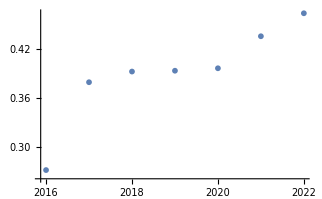

```mathematica
ListPlot[Drop[rearrangedAscendingData]]
```

You can see that all I did was rearrange the data from the different years so that Aaron Judge’s batting average is constantly improving. Apply the program to this data. What are s_x, s_y, and r?

NB: If you didn’t get the same values for s_x and s_y something is wrong. Can you see that s_x and s_y should have been the same?

### 7. Covariance and r-Value One More Time

```mathematica
rearrangedDescendingData = {{"Year", "Average"},{2016,0.463},{2017,0.435},{2018,0.396},{2019,0.393},{2020,0.392},{2021,0.379},{2022,0.272}};
Grid[rearrangedDescendingData]
```

Year | Average
2016 | 0.463
2017 | 0.435
2018 | 0.396
2019 | 0.393
2020 | 0.392
2021 | 0.379
2022 | 0.272

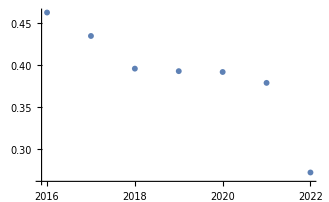

```mathematica
ListPlot[Drop[rearrangedDescendingData]]
```

You can see that all I did was rearrange the data from the different years so that Aaron Judge’s batting average is now constantly deteriorating. Apply the program to this data.

Now what are s_x, s_y, and r?

### Conclusion

You will see r-value and r-squared-value quoted a lot when data is fitted. An r-value near 1 is interpreted as “the data on the y-axis is positively correlated with the data on the x-axis.” An r-value near -1 is interpreted as “the data on the y-axis is negatively correlated with the data on the x-axis.” Often the r-value is squared. Then an r^2-value near 1 means that the data on the y-axis is correlated with the data on the x-axis, but because you have squared r, it is no longer possible to tell whether it is positively or negatively correlated. In all cases an r-value or an r-squared value near 0 means that the values on the x-axis do little to help explain the values on the y-axis. To put it another way, if r is near 0, a simple mean is just as good an approximation to the y-values as a linear fit.

Take a look at the attached pages to develop some additional intuition on r-squared.